```mathematica
M4[s_,u_]:= 1/(s-M^2)+1/(u-M^2)+1/(t-M^2);
```

```mathematica
(* stu k=2 kernel *)
stuK[s_,t_]:=1/((s-4/3 m^2)^2(s-(8/3 m^2-t)));

stuM4[s_,u_]:=M4[s,u]/.{t->4m^2-s-u};

SeriesCoefficient[stuM4[s,u],{s,4/3 m^2,4},{u,4/3 m^2,0}]//FullSimplify
SeriesCoefficient[stuM4[s,u],{s,4/3 m^2,3},{u,4/3 m^2,1}]//FullSimplify
SeriesCoefficient[stuM4[s,u],{s,4/3 m^2,2},{u,4/3 m^2,2}]//FullSimplify
SeriesCoefficient[stuM4[s,u],{s,4/3 m^2,1},{u,4/3 m^2,3}]//FullSimplify
SeriesCoefficient[stuM4[s,u],{s,4/3 m^2,0},{u,4/3 m^2,4}]//FullSimplify
```

486/((4 m^2-3 M^2)^5)

972/((4 m^2-3 M^2)^5)

1458/((4 m^2-3 M^2)^5)

972/((4 m^2-3 M^2)^5)

486/((4 m^2-3 M^2)^5)

```mathematica
(* fwd k=2 kernel *)
K[s_,t_]:=1/((s-2m^2)^2(s-(2m^2-t)));

SeriesCoefficient[(K[M^2,t]-K[4m^2-M^2-t,t])*LegendreP[J,1+(2*t)/(M^2-4m^2)],{t,0,0}]

SeriesCoefficient[(K[M^2,t]-K[4m^2-M^2-t,t])*LegendreP[J,1+(2*t)/(M^2-4m^2)],{t,0,1}]

(* J=0 *)
Series[(K[M^2,t]-K[4m^2-M^2-t,t])*LegendreP[0,1+(2*t)/(M^2-4m^2)],{t,0,1}]
```

-2/((2 m^2-M^2)^3)

-3/((2 m^2-M^2)^4)-(2 J (1+J))/((2 m^2-M^2)^3 (-4 m^2+M^2))

-2/((2 m^2-M^2)^3)-(3 t)/((2 m^2-M^2)^4)+O[t]^2

(3 M^2)/(4 m^2-2 M^2)

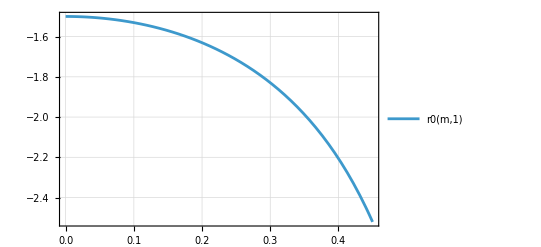

```mathematica
r0[m_,M_]:=(-3/((M^2-2m^2)^4))/(-2/((2m^2-M^2)^3))*M^2

r0[m,M]//FullSimplify

Plot[r0[m,1],{m,0.00,0.45},PlotTheme->"Detailed"]
```

```mathematica
Solve[1/(s-M^2)*a-1/(s-M^2)*LegendreP[0,1+(2t)/(s-4m^2)]==0,{a}]
```

{{a→1}}

```mathematica
M42[s_, t_] := 1/M^4*(((t - u)^2 - (4 m^2 - s)^2/3)/(s-M^2)+((t - s)^2 - (4 m^2 - u)^2/3)/(u-M^2))/.{u -> 4m^2-s-t}
```

```mathematica
b = Residue[M42[s,t]/((s-2m^2)^2(s-(2m^2-t))),{s,2m^2}]+Residue[M42[s,t]/((s-2m^2)^2(s-(2m^2-t))),{s,2m^2-t}]//FullSimplify
```

-(2 (-4 m^2+2 M^2+t) ((-4 m^2+M^2)^2+6 (-4 m^2+M^2) t+6 t^2))/(3 M^4 (-2 m^2+M^2)^2 (-2 m^2+M^2+t)^2)

```mathematica
SeriesCoefficient[b,{t,0,0}]//FullSimplify

SeriesCoefficient[b,{t,0,1}]//FullSimplify
```

-(4 (-4 m^2+M^2)^2)/(3 M^4 (-2 m^2+M^2)^3)

(-32 m^4+32 m^2 M^2-6 M^4)/((-2 m^2 M+M^3)^4)

```mathematica
(* J=2 *)
Series[(K[M^2,t]-K[4m^2-M^2-t,t])*LegendreP[2,1+(2*t)/(M^2-4m^2)],{t,0,1}]
((3 (4 m^2-3 M^2))/((2 m^2-M^2)^4 (4 m^2-M^2)))/(-2/((2 m^2-M^2)^3))//FullSimplify

((-32 m^4+32 m^2 M^2-6 M^4)/((-2 m^2 M+M^3)^4))/(-(4 (-4 m^2+M^2)^2)/(3 M^4 (-2 m^2+M^2)^3))//FullSimplify
```

-2/((2 m^2-M^2)^3)+(3 (4 m^2-3 M^2) t)/((2 m^2-M^2)^4 (4 m^2-M^2))+O[t]^2

-(3 (4 m^2-3 M^2))/(2 (8 m^4-6 m^2 M^2+M^4))

-(3 (4 m^2-3 M^2))/(2 (8 m^4-6 m^2 M^2+M^4))

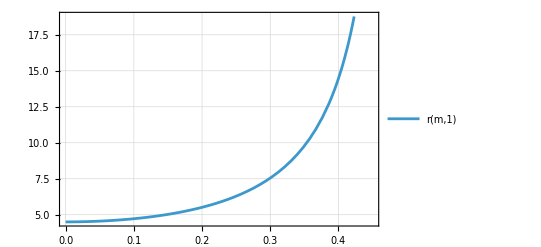

g3[0.4,  1]/g2[0.4,  1]*M^2=14.4608

```mathematica
r[m_,M_]:=((3 (4 m^2-3 M^2))/((2 m^2-M^2)^4 (4 m^2-M^2)))/(-2/((2 m^2-M^2)^3));

Plot[r[m,1],{m,0.0,0.45},PlotTheme->"Detailed"]

Print["g3[0.4,  1]/g2[0.4,  1]*M^2=", r[0.40,1]];
```

```mathematica
stuM42[s_, u_] := 1/M^4*(((t - u)^2 - (4 m^2 - s)^2/3)/(s-M^2)+((t - s)^2 - (4 m^2 - u)^2/3)/(u-M^2)+((s - u)^2 - (4 m^2 - t)^2/3)/(t-M^2))/.{t -> 4m^2-s-u}
```

```mathematica
SeriesCoefficient[stuM42[s,u],{s,4/3 m^2,4},{u,4/3 m^2,0}]//FullSimplify
SeriesCoefficient[stuM42[s,u],{s,4/3 m^2,3},{u,4/3 m^2,1}]//FullSimplify
SeriesCoefficient[stuM42[s,u],{s,4/3 m^2,2},{u,4/3 m^2,2}]//FullSimplify
SeriesCoefficient[stuM42[s,u],{s,4/3 m^2,1},{u,4/3 m^2,3}]//FullSimplify
SeriesCoefficient[stuM42[s,u],{s,4/3 m^2,0},{u,4/3 m^2,4}]//FullSimplify
```

(324 (-(16 m^4)/3+M^4))/(M^4 (4 m^2-3 M^2)^5)

(216 (16 m^4-3 M^4))/(M^4 (-4 m^2+3 M^2)^5)

(324 (16 m^4-3 M^4))/(M^4 (-4 m^2+3 M^2)^5)

(216 (16 m^4-3 M^4))/(M^4 (-4 m^2+3 M^2)^5)

(108 (16 m^4-3 M^4))/(M^4 (-4 m^2+3 M^2)^5)

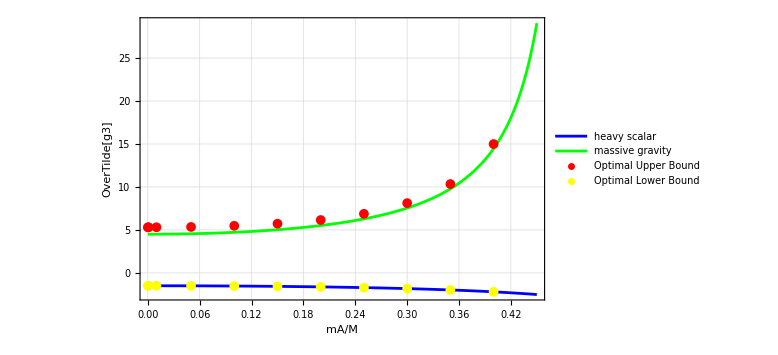

```mathematica
(* Plot of spin-0 and spin-2 scattering with SDPB result *)
data1={{0`200,5.30624354498155`200},{0.001`200,5.30625916733434`200},{0.01`200,5.30781869969842`200},{0.05`200,5.34630310757489`200},{0.1`200,5.47538008276237`200},{0.15`200,5.72277490276586`200},{0.2`200,6.15033989170755`200},{0.25`200,6.87207325126097`200},{0.3`200,8.11853267109362`200},{0.35`200,10.337098209359`200},{0.4`200,14.9939610708506`200}};

data2 = {{0`200,-1.4999999999985`200},{0.001`200,-1.50000062016405`200},{0.01`200,-1.5003000600105`200},{0.05`200,-1.50753768844069`200},{0.1`200,-1.53061224489639`200},{0.15`200,-1.5706806282706`200},{0.2`200,-1.63043478260692`200},{0.25`200,-1.71428571428375`200},{0.3`200,-1.82926829268069`200},{0.35`200,-1.98675496688478`200},{0.4`200,-2.20588235293793`200}};

p1=ListPlot[data1,PlotStyle->{Red,PointSize[0.001]},PlotMarkers->{"●",10},PlotRange->All,PlotTheme->"Detailed",PlotLegends->{"Optimal Upper Bound"}];

p2=Plot[{r0[m,1`200],r[m,1`200]},{m,0`200,0.45`200},PlotStyle->{Blue,Green},PlotRange->All,WorkingPrecision->200,PlotTheme->"Detailed",PlotLegends->{"heavy scalar","massive gravity"}];

p3=ListPlot[data2,PlotStyle->{Yellow,PointSize[0.001]},PlotMarkers->{"●",10},PlotRange->All,PlotTheme->"Detailed",PlotLegends->{"Optimal Lower Bound"}];

plot=Show[p2,p1,p3,Frame->True,FrameLabel->{Style[TraditionalForm[mA/M],16],Style[TraditionalForm[Overscript[g3,"~"]],16]},PlotRange->All,ImageSize->Large]
```

```mathematica
Export["C:\\Users\\User\\Pictures\\Screenshots\\plot.png",plot]
```

C:\Users\User\Pictures\Screenshots\plot.png